Data Import

```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210407_sliding_time_windows_and_OR_model"];
```

```mathematica
Get["../algoritm_packages/SingleNetworks-algorithm-package.wl"]
(* ?SingleNetworks`* *)
```

```mathematica
datafull=Import["../data/ccm_manipulated_396096.csv",HeaderLines->1];
```

Data with Sliding Time Windows

```mathematica
x1=Round@Ceiling[Length@datafull/10,1];
{a,b,c,d,e,f,g,h,i,j}=Join[Range[x1,Length@datafull,x1],{Length@datafull}];
data1=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x1/2,z[[2]]-x1/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j},2,1]}],1]];
win1=Length@data1;
```

```mathematica
x2=Round@Ceiling[Length@datafull/21,1];
{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v}=Join[Range[x2,Length@datafull,x2],{Length@datafull}];
data2=Join[{Take[datafull,{1,a}]},Flatten[Table[{Take[datafull,{z[[1]]-x2/2,z[[2]]-x2/2}],Take[datafull,{z[[1]],z[[2]]}]},{z,
Partition[{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,r,s,t,u,v},2,1]}],1]];
win2=Length@data2;
```

Investigation of Constraints Impact in Time Windows

Fixed Step Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,9,11,win1];]
```

{116.244,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep1[[1]][[i]],widthdataintimewindowsFixedstep1[[2]][[i]],2,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{403.842,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,9,11,win2];]
```

{117.223,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedstep2[[1]][[i]],widthdataintimewindowsFixedstep2[[2]][[i]],2,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{646.764,Null}

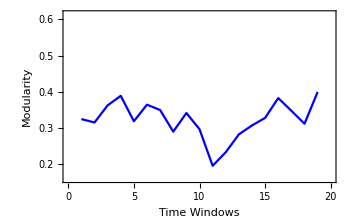
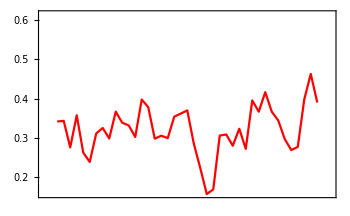
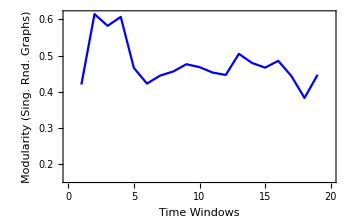
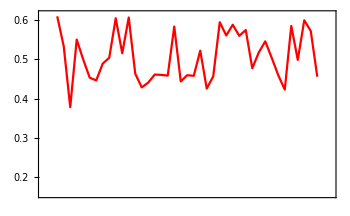
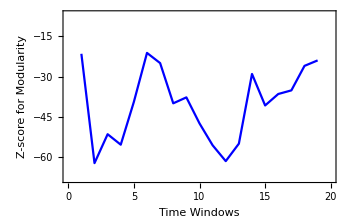
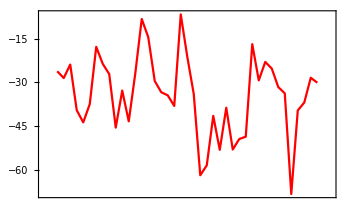

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{modularityvalues1,singlerandomcommmodularityvalues1,modularityvalues2,singlerandomcommmodularityvalues2}]}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep1=snetworkdatabinnedintimewindows[data1,10,1,win1];]
```

{31.2518,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep1[[1]][[i]],thicknessdataintimewindowsFixedstep1[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{247.036,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedstep2=snetworkdatabinnedintimewindows[data2,10,1,win2];]
```

{28.2049,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedstep2[[1]][[i]],thicknessdataintimewindowsFixedstep2[[2]][[i]],2,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{342.152,Null}

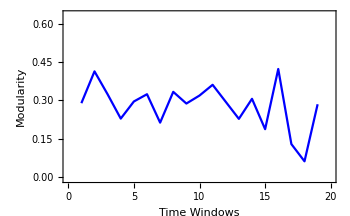
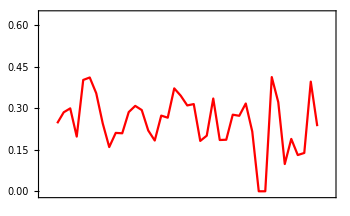
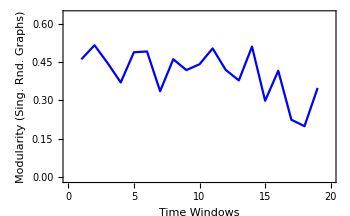
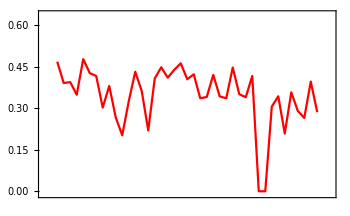
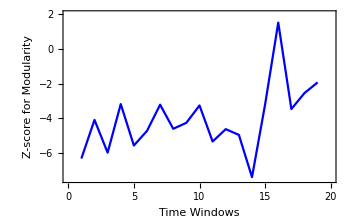
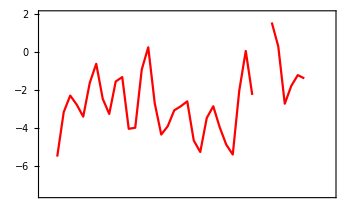

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-7.5,2}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-7.5,2}}]}]}
```

Fixed Bucket Size Networks

Width Feature

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,9,85,win1];]
```

{17.5339,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket1[[1]][[i]],widthdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,Green],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{408.187,Null}

```mathematica
AbsoluteTiming[widthdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,9,85,win2];]
```

{20.0548,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[widthdataintimewindowsFixedbucket2[[1]][[i]],widthdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,Green],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{783.516,Null}

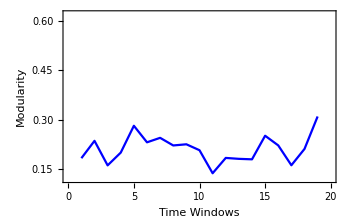
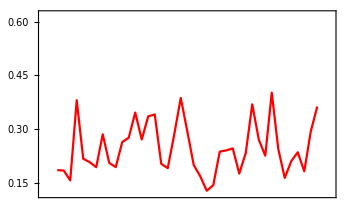
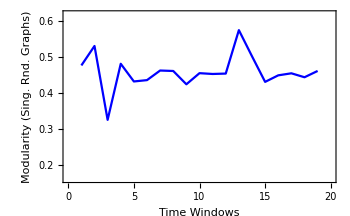
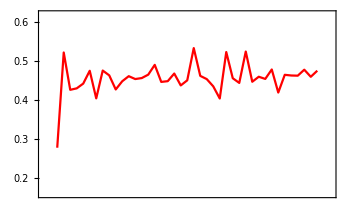
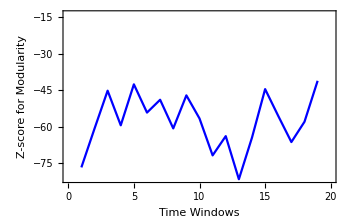
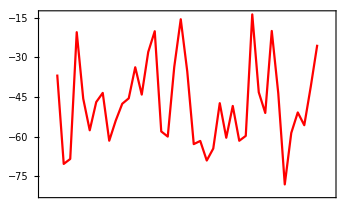

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.12,0.62}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.12,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{0.16,0.62}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{0.16,0.62}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},MinMax[{Zscoresmodularity1,Zscoresmodularity2}]}]}]}
```

Thickness Feature

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket1=snetworkdatafxdbucketintimewindows[data1,10,20,win1];]
```

{11.5568,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket1[[1]][[i]],thicknessdataintimewindowsFixedbucket1[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win1}];
modularityvalues1=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues1=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity1=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{207.528,Null}

```mathematica
AbsoluteTiming[thicknessdataintimewindowsFixedbucket2=snetworkdatafxdbucketintimewindows[data2,10,20,win2];]
```

{11.9498,Null}

```mathematica
graphsandnodenumbers=Table[snetworkgraph[thicknessdataintimewindowsFixedbucket2[[1]][[i]],thicknessdataintimewindowsFixedbucket2[[2]][[i]],1.5,7,400,RGBColor[0.1,0.5,1.]],{i,Range@win2}];
modularityvalues2=Table[N@GraphAssortativity[graphsandnodenumbers[[i]][[1]],FindGraphCommunities[graphsandnodenumbers[[i]][[1]]],"Normalized"->False],{i,Length@graphsandnodenumbers}];
singlerandomgraphscomm=Table[randomizedgraphamongcommunities[i],{i,graphsandnodenumbers[[All,1]]}];
singlerandomcommmodularityvalues2=Table[N@GraphAssortativity[singlerandomgraphscomm[[i]],FindGraphCommunities[singlerandomgraphscomm[[i]]],"Normalized"->False],{i,Length@singlerandomgraphscomm}];
AbsoluteTiming[Zscoresmodularity2=Table[randomnessfunctionformodularityonenullmodel[i],{i,graphsandnodenumbers[[All,1]]}];]
```

{494.121,Null}

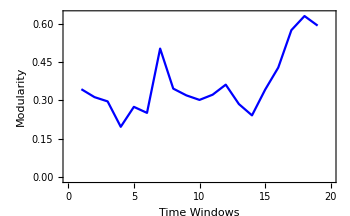
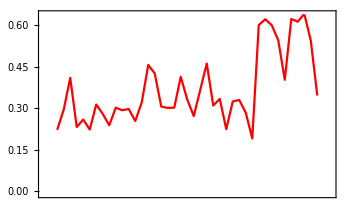
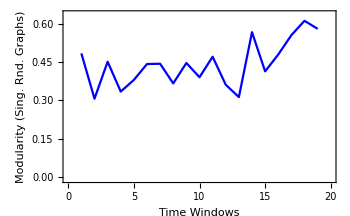
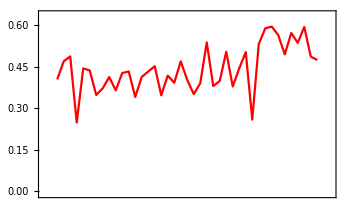
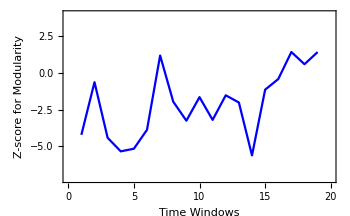
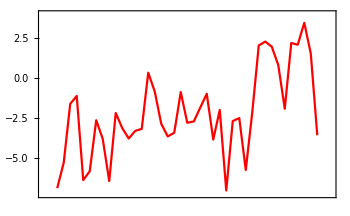

```mathematica
{Overlay[{ListLinePlot[Thread[{Range@win1,modularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,modularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,singlerandomcommmodularityvalues1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Modularity (Sing. Rnd. Graphs)",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-0.01,0.64}}],ListLinePlot[Thread[{Range@win2,singlerandomcommmodularityvalues2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-0.01,0.64}}]}],
Overlay[{ListLinePlot[Thread[{Range@win1,Zscoresmodularity1}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{All,None}},FrameLabel->{{"Z-score for Modularity",None},{Style["Time Windows",Blue],None}},PlotStyle->Blue,ImageSize->350,PlotRange->{{0,win1+1},{-7.25,4}}],ListLinePlot[Thread[{Range@win2,Zscoresmodularity2}],Frame->True,ImagePadding->38,FrameTicks->{{All,None},{None,All}},FrameLabel->{{None,None},{None,Style["Time Windows",Red]}},PlotStyle->Red,ImageSize->350,PlotRange->{{0-1,win2+2},{-7.25,4}}]}]}
```

Plots for Network Metrics and Z-scores

Modeling Works with OR Methods

FBA Model Reproducing from Kauffman et al. 2003

```mathematica
stochmatrix={{-1,-1,1,0,1,0,0},{1,0,0,1,0,-1,0},{0,1,-1,-1,0,0,-1}};
objectivefunc1={2,0,0,1,0,0,0};
objectivefunc2={1,0,0,2,0,0,0};
boundaries={{0,Infinity},{0,Infinity},{0,0},{0,Infinity},{0,1},{0,2},{0,0}};
steadystatevector={{0,0},{0,0},{0,0}};
Vvector={v1,v2,v3,v4,b1,b2,b3};
```

stochmatrix . Vvector = steadystatevector  ,   -objectivefunc ∈ solution space within boundaries
A, B, and C are metabolites. , , , and  are reactions. , , and  are flux exchanges.

```mathematica
Print["1st objective function solution vector: ",Vvector1=LinearProgramming[-objectivefunc1,stochmatrix,steadystatevector,boundaries]]
Print["2nd objective function solution vector: ",Vvector2=LinearProgramming[-objectivefunc2,stochmatrix,steadystatevector,boundaries]]
```

1st objective function solution vector: {1,0,0,0,1,1,0}

2nd objective function solution vector: {0,1,0,1,1,1,0}

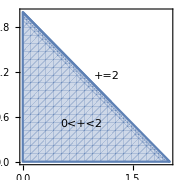

```mathematica
Show[RegionPlot[0<+<2,{,0,2},{,0,2},Frame->True,PlotLabels->Placed["0<+<2",{0.8,0.5}],FrameLabel->{"",""}],Plot[-+2,{,0,1.2},Frame->True,PlotLabels->Placed["+=2",{1.1,1}]],PlotRange->All,ImageSize->Small]
```

```mathematica
FindMaximum[{v4+2v1,-v1-v2+v3+b1==0&&v1+v4-b2==0&&v2-v3-v4-b3==0&&0≤v1+v2≤1&&0≤v1+v4≤2&&v2-v4==0&&0≤b1≤1&&0≤b2≤2&&b3==0&&v1≥0&&v2≥0&&v3==0&&v4≥0},{v1,v2,v3,v4,b1,b2,b3}]
```

{2.,{v1→1.,v2→0.,v3→0.,v4→0.,b1→1.,b2→1.,b3→0.}}

```mathematica
AdjmatR=Transpose[stochmatrix].stochmatrix;
NormAdjmatR=AdjmatR/.x_/;x≠0->1;
AdjmatM=stochmatrix.Transpose[stochmatrix];
NormAdjmatM=AdjmatM/.x_/;x≠0->1;
```

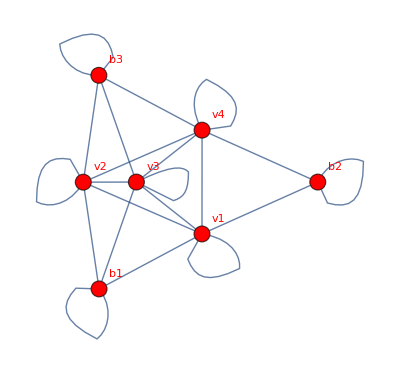
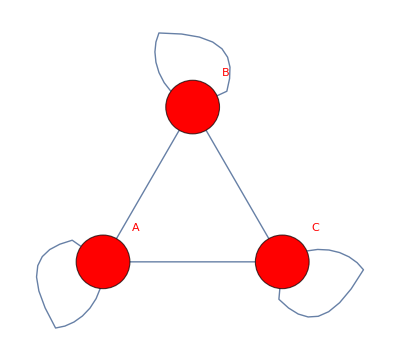

```mathematica
{AdjacencyGraph[NormAdjmatR,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"v1",2->"v2",3->"v3",4->"v4",5->"b1",6->"b2",7->"b3"}}],AdjacencyGraph[NormAdjmatM,{DirectedEdges->False,VertexSize->0.3,VertexStyle->Red,VertexLabels->{1->"A",2->"B",3->"C"}}]}
```

Implementation Trials

```mathematica
stoichioforhomosapiens=Drop[Import["../210324_disc_time_windows_and_OR_model/iAT_PLT_636_stoichiomat.csv",HeaderLines->1],None,{1}];
SparseArray@stoichioforhomosapiens
```

SparseArray[…]

```mathematica
stoichiometricmatrix=stoichioforhomosapiens;
metabolites=738;
fluxexchanges=1008;
steadystatevector=ConstantArray[{0,0},metabolites];
boundaries=ConstantArray[{0,500},fluxexchanges];
```

```mathematica
syntheticseqgenerator[stoichiometricmatrix_,steadystatevector_,boundaries_,fluxexchanges_,sequencesize_]:=Module[{subsetsizechoice,subsetpositions,coefficients,objectivefunctions,solutionvectors},
subsetsizechoice=RandomInteger[{1,fluxexchanges}];
subsetpositions=RandomSample[Range@fluxexchanges,subsetsizechoice];
coefficients=Table[RandomReal[{-2,2},subsetsizechoice],sequencesize];
objectivefunctions=Table[ReplacePart[ConstantArray[0.,fluxexchanges],MapThread[#1->#2&,{subsetpositions,coefficients[[i]]}]],{i,sequencesize}];
solutionvectors=Table[LinearProgramming[-objectivefunctions[[i]],stoichiometricmatrix,steadystatevector,boundaries],{i,Length@objectivefunctions}]]
```

```mathematica
SeedRandom@5;
AbsoluteTiming[sequences=Table[syntheticseqgenerator[stoichiometricmatrix,steadystatevector,boundaries,fluxexchanges,300],200];]
```

```mathematica
Print["Data Dimension: ",Dimensions@Flatten[sequenceschopped,1]]
Print["Unique Row Amount: ",Length@(Flatten[sequenceschopped,1])[[first@Flatten[sequenceschopped,1],All]]]
Print["Unique Column Amount: ",(Dimensions@testcolumns)[[2]]]
```

Data Dimension: {60000,1008}

Unique Row Amount: 38007

Unique Column Amount: 3

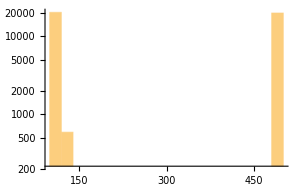
{-Graphics-,-Graphics-}

```mathematica
Table[Histogram[datachopped[[All,i]],ScalingFunctions->"Log",PlotRange->All,ImageSize->300],{i,{3,4}}]
```

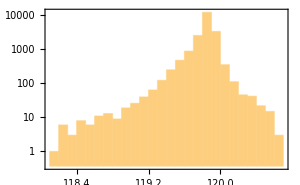
{-Graphics-,-Graphics-}

{{-Graphics-,54},{-Graphics-,42},{-Graphics-,31},{-Graphics-,28},{-Graphics-,28},{-Graphics-,27},{-Graphics-,26},{-Graphics-,24},{-Graphics-,36},{-Graphics-,36},{-Graphics-,36},{-Graphics-,36},{-Graphics-,29},{-Graphics-,21},{-Graphics-,18},{-Graphics-,25},{-Graphics-,26},{-Graphics-,43},{-Graphics-,43},{-Graphics-,42},{-Graphics-,42},{-Graphics-,11},{-Graphics-,25},{-Graphics-,81},{-Graphics-,116},{-Graphics-,106},{-Graphics-,40},{-Graphics-,31},{-Graphics-,31},{-Graphics-,40},{-Graphics-,52},{-Graphics-,55},{-Graphics-,18},{-Graphics-,38},{-Graphics-,39},{-Graphics-,41},{-Graphics-,47}}

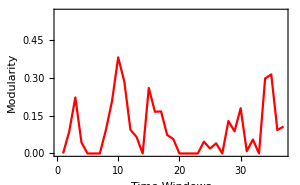
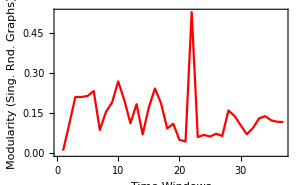
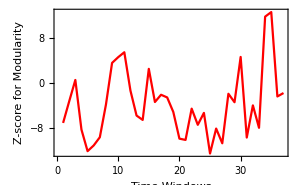

{{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30},{-Graphics-,30}}

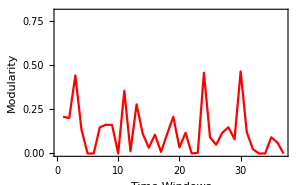
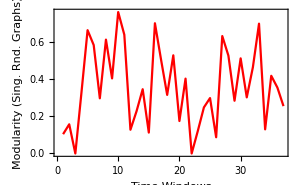
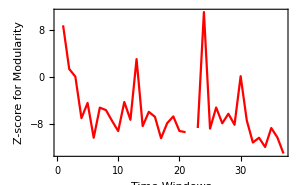

```mathematica
Table[Histogram[datachoppedfinal[[All,i]],ScalingFunctions->"Log",Frame->True,PlotRange->All,ImageSize->300],{i,{3,4}}]
```